## Large Field Potential Perturbation Plot

```mathematica
makeColorList[aList_,col_]:=Module[{posList,negList,a2List,cList},
posList=Sort[Select[aList,#>0&]];
negList=Sort[Select[aList,#<0&]];
cList={};
Do[AppendTo[cList,Darker[Blue,i/(1.5*Length[negList])]];,{i,1,Length[negList]}];
AppendTo[cList,Black];
Do[AppendTo[cList,Darker[col,i/(1.5*Length[posList])]];,{i,Length[posList],1,-1}];
a2List = Join[negList,{0},posList];
Return[{a2List,cList}]]
```

```mathematica
makeColorListLegend[aList_,col_,label_,var_]:=Module[{a2List,cList,legend},
a2List=Sort[aList];
cList={};
(*Do[AppendTo[cList,Darker[col,i/(1.5*Length[a2List])]];,{i,Length[a2List],1,-1}];*)
Do[AppendTo[cList,Blend[{col,Black},i/(Length[a2List])]];,{i,Length[a2List],1,-1}];
legend=Graphics[{Table[{Blend[{cList[[1]],cList[[-1]]},x/Length[cList]],Rectangle[{x,0}]},{x,1,Length[cList],1}],Table[Text[Style[a2List[[x]],Large],{x+0.5,1.25}],{x,1,Length[a2List],1}],Text[label,{0,0.5}],Text[var,{0.75,1.25}]}];
Return[{a2List,cList,legend}]]
```

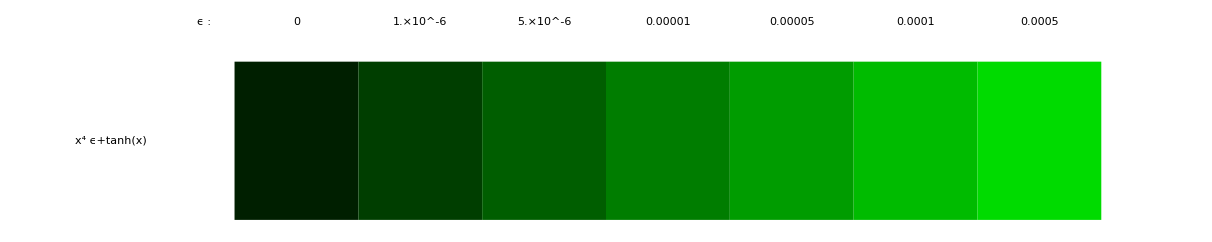

```mathematica
a1List ={0,0.000001,0.00001,0.0001,0.000005,0.00005,0.0005};
v[x_]:=Tanh[x]+ϵ*x^4;
{a2List,cList,legend}=makeColorListLegend[a1List,Green,Text[Style[v[x],Large]],Text[Style["ϵ :",Large]]];
legend
```

```mathematica
perturbPlot[v0_,a0List_,col_]:=Module[{aList,cList,nsList,rList,pltList,ii,nsmin,nsmax,rmin,rmax,v1,v2,v,ni,nf,ni2,nf2,n1guess,left,ϕsol2,ns,r,ϵ2,legend},
{aList,cList,legend} = makeColorListLegend[a0List,col,Text[Style[v0[x]+ϵ*x^4,Large]],Text[Style["ϵ :",Large]]];
nsList={}; rList={};
pltList={}; ii=1;
nsmin = 0.95; nsmax = 1; rmin = 10^-4; rmax = 0.01;
Do[
v1=vacuumShift[v0];
v[x_]:=v1[x]+aList[[ii]]*x^4;
Print[Plot[v[x],{x,-5,10}]];
v2=vacuumShift[v];
Print[Plot[v2[x],{x,-5,10}]]; 
ni = 80; (* initial value f n for integration *)
nf = -1.5; (* final value of n for integration *)
ni2 = 80;
nf2 = 0;
n1guess = -1;
left = False;
ϕsol2=CheckAbort[findϕsol[v,v',v'',ni,nf,ni2,nf2,n1guess,False,False, left],Print["ABORTED"];Continue[]];
(*If[%===$Aborted,Print["ABORTED"],*)
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,True];
AppendTo[nsList,ns/.{n->60}];
AppendTo[rList,r/.{n->60}];
(*AppendTo[pltList,ListLogPlot[Legended[Thread[{{ns/.n->60},{r/.n->60}}],aList[[ii]]],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,20},PlotStyle->cList[[ii]]]];*)
AppendTo[pltList,ListLogPlot[Thread[{{ns/.n->60},{r/.n->60}}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{Style["ns",FontSize->24],Style["r",FontSize->24]},PlotMarkers->{●,20},PlotStyle->cList[[ii]],TicksStyle->Directive[FontSize->20]]];
,{ii,Length[aList]}];
Return[{aList,nsList,rList,pltList,legend}]]
```

NMinimize::ubnd: The problem is unbounded.

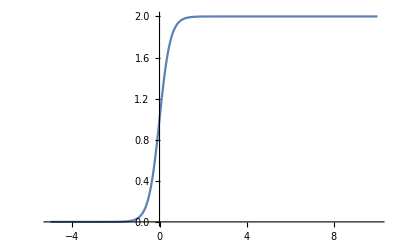

NMinimize::ubnd: The problem is unbounded.

-Graphics-

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕ0list = {0.150864}

vacuumArray = {}

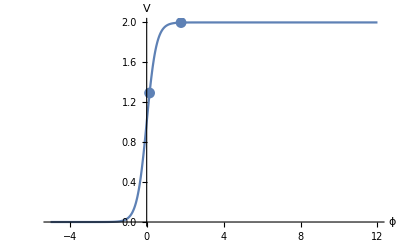

InterpolatingFunction::dmval: Input value {-9.0019} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.80019} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.99416} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

At n = 0, ϵ1 = 0.951134

ns[60] = 0.965893

r[60] = 0.000147208

NMinimize::ubnd: The problem is unbounded.

General::stop: Further output of NMinimize :: ubnd will be suppressed during this calculation.

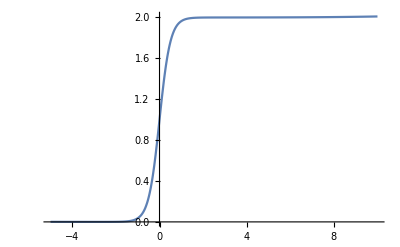

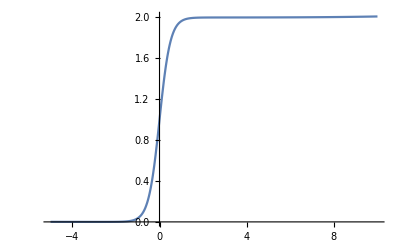

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕ0list = {-2.62886,0.150864}

vacuumArray = {}

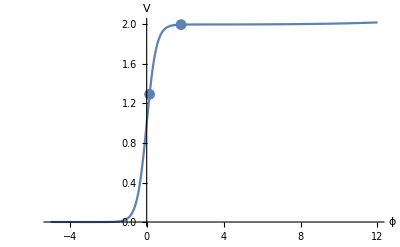

At n = 0, ϵ1 = 0.953067

ns[60] = 0.96596

r[60] = 0.000147616

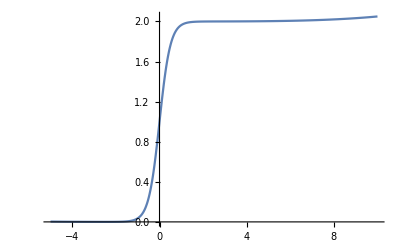

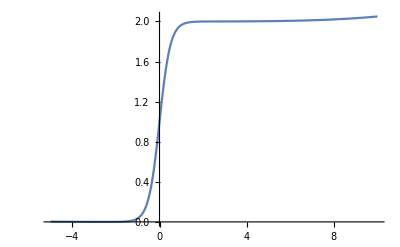

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

ϕ0list = {-2.33077,0.150864}

vacuumArray = {}

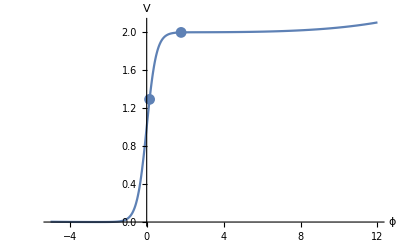

At n = 0, ϵ1 = 0.953548

ns[60] = 0.96622

r[60] = 0.000149251

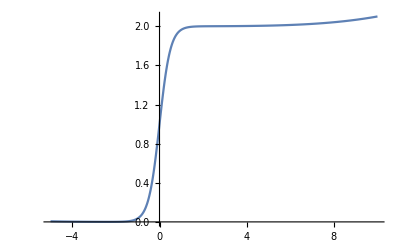

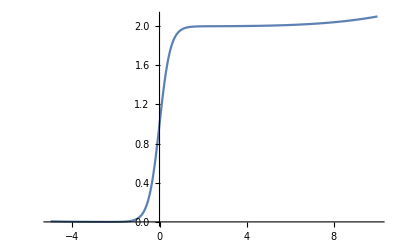

ϕ0list = {-2.20516,0.150864}

vacuumArray = {}

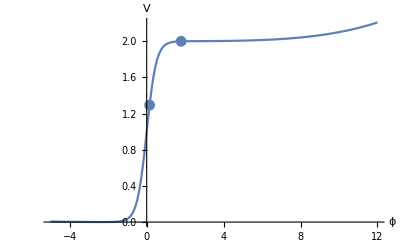

At n = 0, ϵ1 = 0.970472

ns[60] = 0.966559

r[60] = 0.000151347

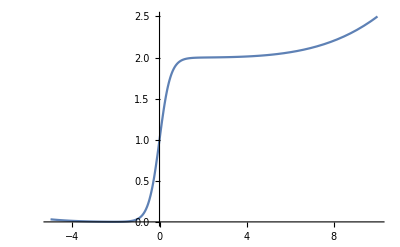

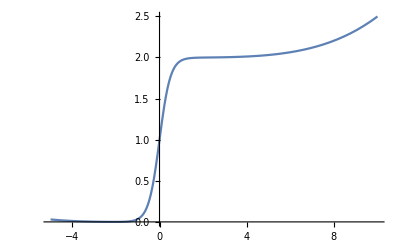

ϕ0list = {-1.92072,0.150864}

vacuumArray = {}

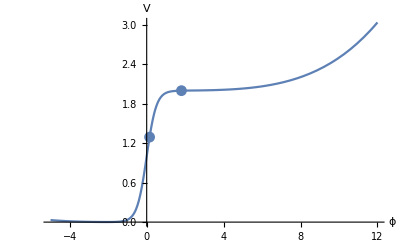

At n = 0, ϵ1 = 0.959614

ns[60] = 0.969251

r[60] = 0.000169014

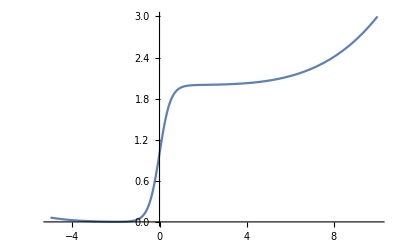

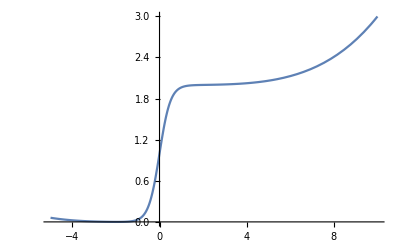

ϕ0list = {-2.774,-2.35625,-1.80161,0.150864}

vacuumArray = {}

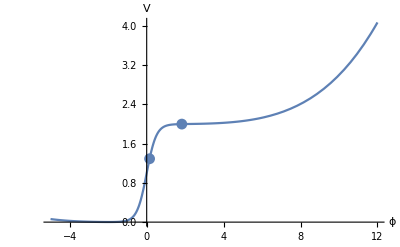

At n = 0, ϵ1 = 0.970895

ns[60] = 0.972646

r[60] = 0.000194237

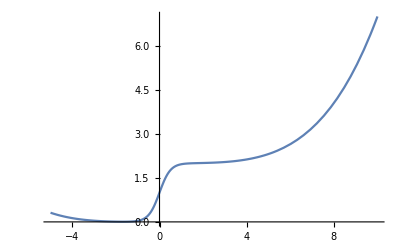

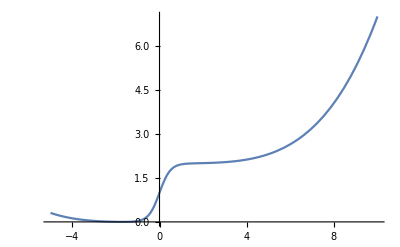

ϕ0list = {-2.8198,-1.94136,-1.53389,0.150865}

vacuumArray = {}

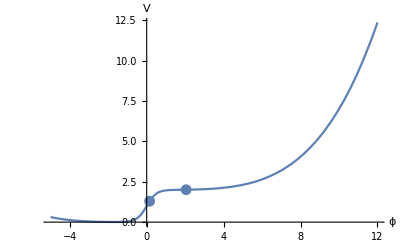

At n = 0, ϵ1 = 2.51941

ns[60] = 1.00106

r[60] = 0.000613189

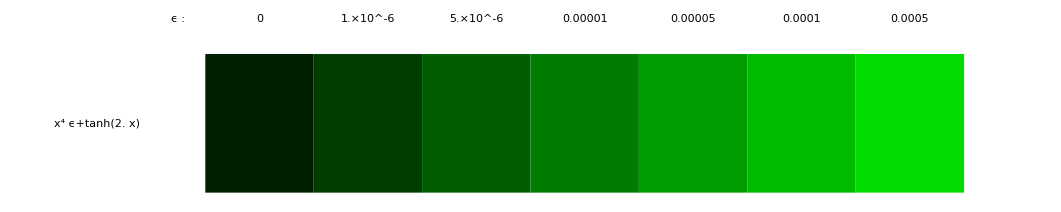

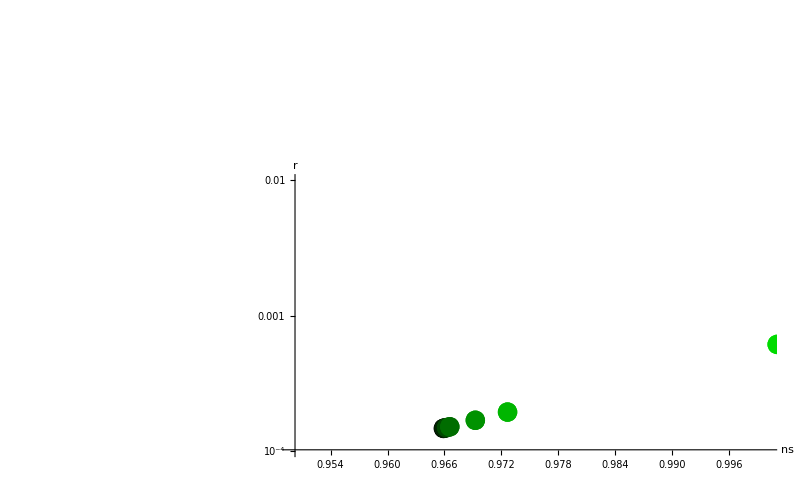

```mathematica
a1List ={0,0.000001,0.00001,0.0001,0.000005,0.00005,0.0005};
v[x_]:=Tanh[x/0.5];
{aList,nsList,rList,pltList,legend}=perturbPlot[v,a1List,Green];
legend
Show[pltList,legend]
```

Minimize::natt: The minimum is not attained at any point satisfying the given constraints.

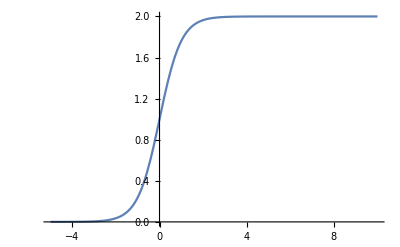

Minimize::natt: The minimum is not attained at any point satisfying the given constraints.

-Graphics-

ϕ0list = {-0.440687}

vacuumArray = {}

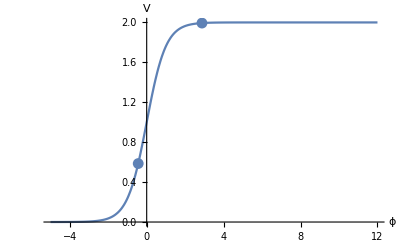

InterpolatingFunction::dmval: Input value {-3.08467} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2.02003} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2.04429} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

At n = 0, ϵ1 = 1.00303

ns[60] = 0.965287

r[60] = 0.000611975

Minimize::natt: The minimum is not attained at any point satisfying the given constraints.

General::stop: Further output of Minimize :: natt will be suppressed during this calculation.

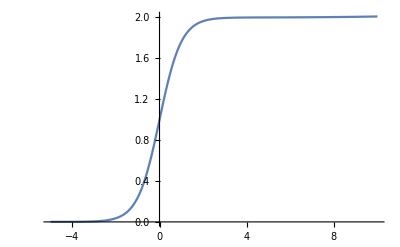

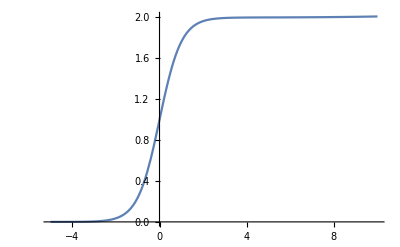

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕ0list = {-3.84391,-0.440688}

vacuumArray = {}

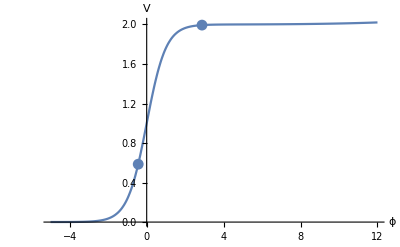

At n = 0, ϵ1 = 1.003

ns[60] = 0.965438

r[60] = 0.000615398

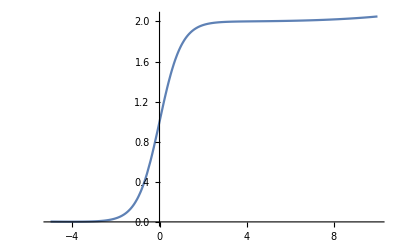

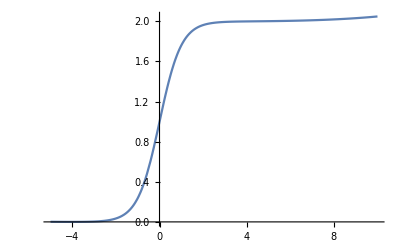

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕ0list = {-3.3056,-0.440691}

vacuumArray = {}

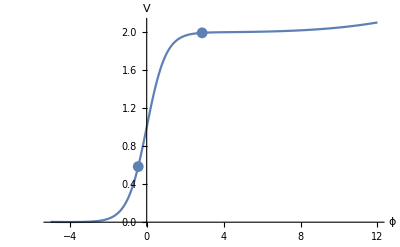

At n = 0, ϵ1 = 1.56151

ns[60] = 0.965579

r[60] = 0.000645412

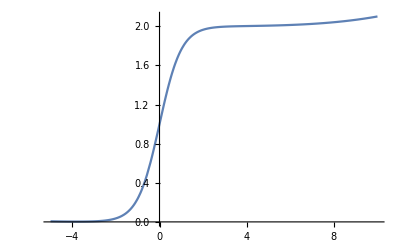

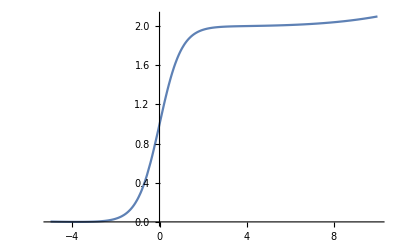

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

ϕ0list = {-3.08134,-0.440695}

vacuumArray = {}

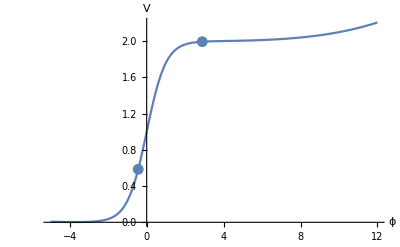

At n = 0, ϵ1 = 1.56131

ns[60] = 0.966308

r[60] = 0.000663622

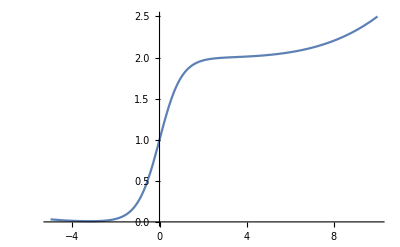

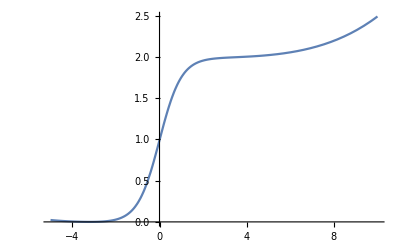

ϕ0list = {-2.57955,-0.440728}

vacuumArray = {}

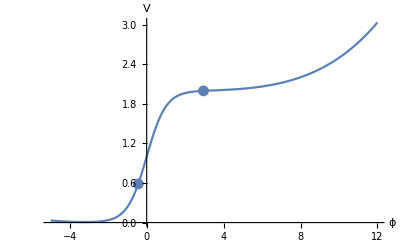

At n = 0, ϵ1 = 1.00051

ns[60] = 0.972811

r[60] = 0.000811171

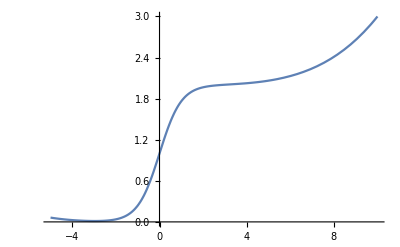

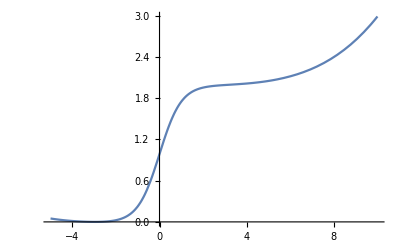

ϕ0list = {-2.37188,-0.440768}

vacuumArray = {}

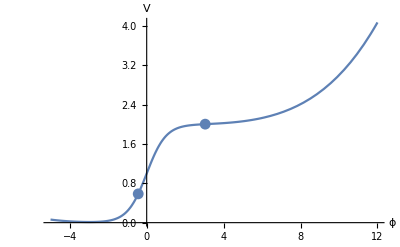

At n = 0, ϵ1 = 1.00132

ns[60] = 0.980616

r[60] = 0.00108185

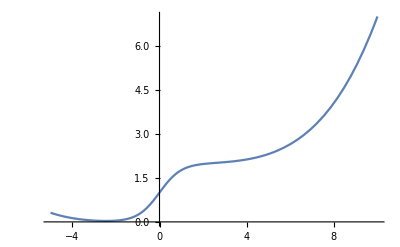

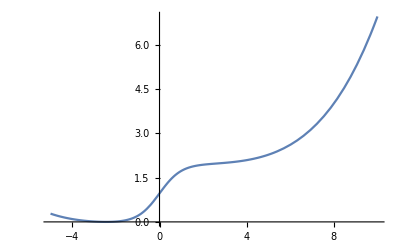

ϕ0list = {-1.90941,-0.441096}

vacuumArray = {}

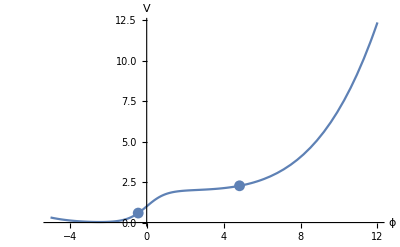

At n = 0, ϵ1 = 1.

ns[60] = 1.05775

r[60] = 0.0143378

NMinimize::ubnd: The problem is unbounded.

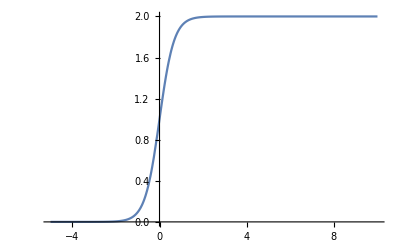

NMinimize::ubnd: The problem is unbounded.

-Graphics-

ϕ0list = {0.038169}

vacuumArray = {}

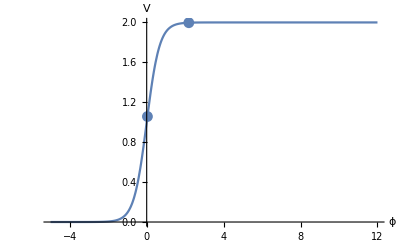

At n = 0, ϵ1 = 0.984195

ns[60] = 0.965755

r[60] = 0.000264046

NMinimize::ubnd: The problem is unbounded.

General::stop: Further output of NMinimize :: ubnd will be suppressed during this calculation.

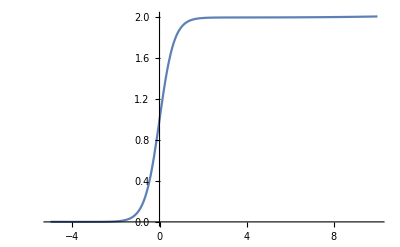

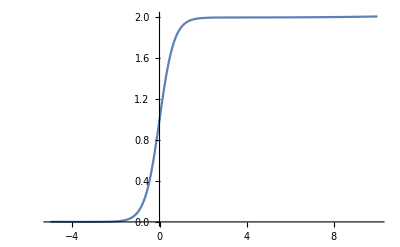

ϕ0list = {-3.13607,0.038169}

vacuumArray = {}

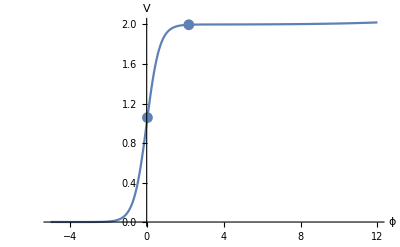

At n = 0, ϵ1 = 0.985222

ns[60] = 0.965849

r[60] = 0.000265049

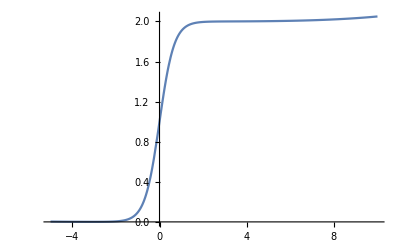

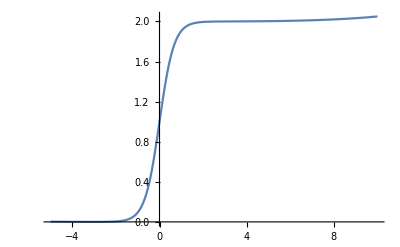

ϕ0list = {-2.75217,0.038169}

vacuumArray = {}

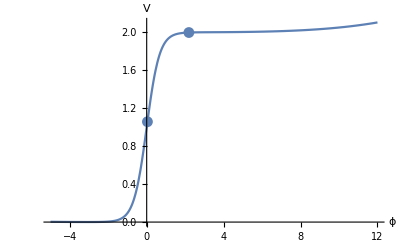

At n = 0, ϵ1 = 2.20085

ns[60] = 0.965887

r[60] = 0.000274401

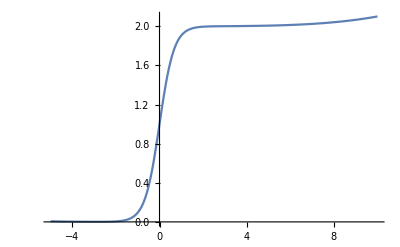

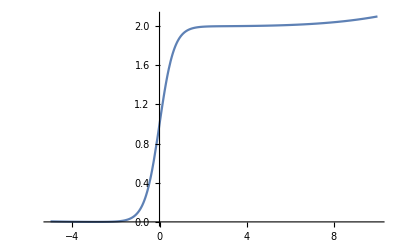

ϕ0list = {-2.59106,0.038169}

vacuumArray = {}

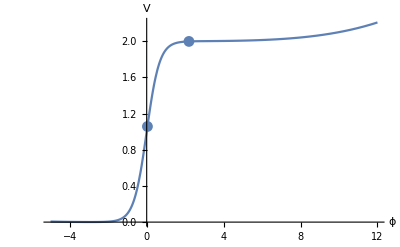

At n = 0, ϵ1 = 2.1865

ns[60] = 0.966361

r[60] = 0.000279472

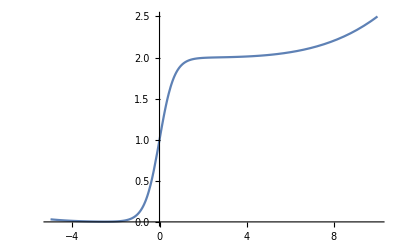

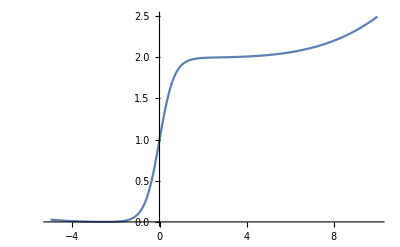

ϕ0list = {-2.2279,0.038169}

vacuumArray = {}

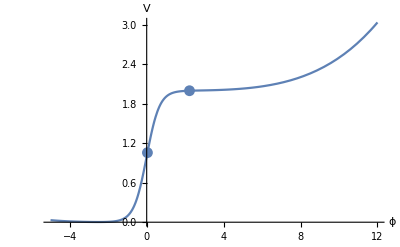

At n = 0, ϵ1 = 2.3552

ns[60] = 0.970077

r[60] = 0.000326088

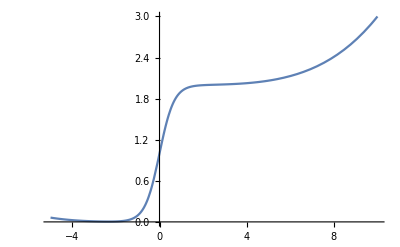

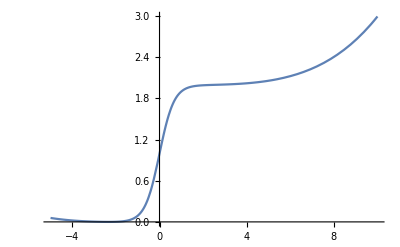

ϕ0list = {-2.07661,0.038169}

vacuumArray = {}

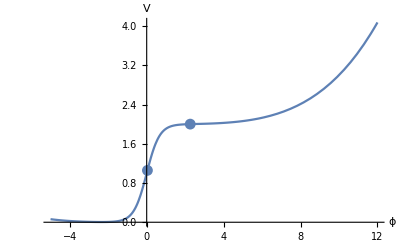

At n = 0, ϵ1 = 2.11068

ns[60] = 0.975041

r[60] = 0.000391883

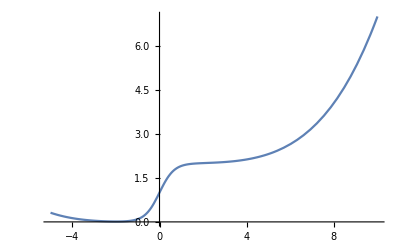

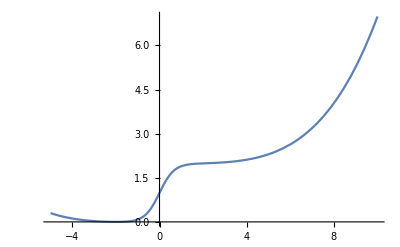

ϕ0list = {-1.73839,0.038169}

vacuumArray = {}

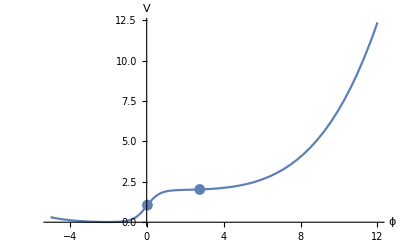

At n = 0, ϵ1 = 0.999866

ns[60] = 1.01865

r[60] = 0.00197274

-Graphics-

-Graphics-

ϕ0list = {0.150864}

vacuumArray = {}

-Graphics-

At n = 0, ϵ1 = 0.953607

ns[60] = 0.96589

r[60] = 0.000147211

-Graphics-

-Graphics-

ϕ0list = {-2.62886,0.150864}

vacuumArray = {}

-Graphics-

At n = 0, ϵ1 = 0.953067

ns[60] = 0.96596

r[60] = 0.000147616

-Graphics-

-Graphics-

ϕ0list = {-2.33077,0.150864}

vacuumArray = {}

-Graphics-

At n = 0, ϵ1 = 0.953548

ns[60] = 0.96622

r[60] = 0.000149251

-Graphics-

-Graphics-

ϕ0list = {-2.20516,0.150864}

vacuumArray = {}

-Graphics-

At n = 0, ϵ1 = 0.970472

ns[60] = 0.966559

r[60] = 0.000151347

-Graphics-

-Graphics-

ϕ0list = {-1.92072,0.150864}

vacuumArray = {}

-Graphics-

At n = 0, ϵ1 = 0.959614

ns[60] = 0.969251

r[60] = 0.000169014

-Graphics-

-Graphics-

ϕ0list = {-2.774,-2.35625,-1.80161,0.150864}

vacuumArray = {}

-Graphics-

At n = 0, ϵ1 = 0.970895

ns[60] = 0.972646

r[60] = 0.000194237

-Graphics-

-Graphics-

ϕ0list = {-2.8198,-1.94136,-1.53389,0.150865}

vacuumArray = {}

-Graphics-

At n = 0, ϵ1 = 2.51941

ns[60] = 1.00106

r[60] = 0.000613189

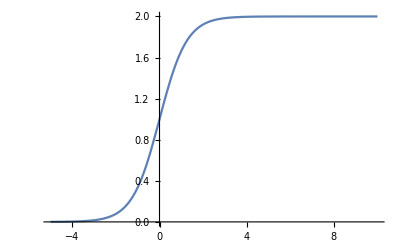

-Graphics-

ϕ0list = {-1.26858}

vacuumArray = {}

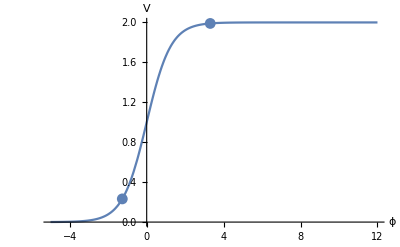

At n = 0, ϵ1 = 0.998126

ns[60] = 0.964611

r[60] = 0.000996633

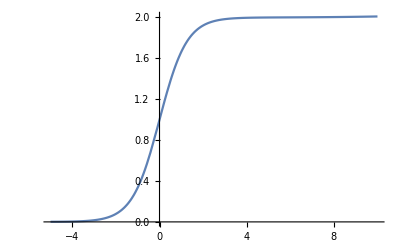

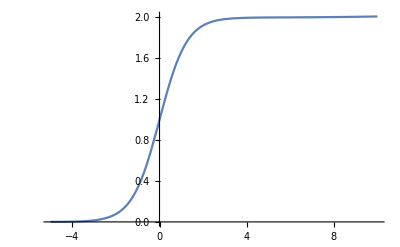

ϕ0list = {-3.99308,-1.26878}

vacuumArray = {}

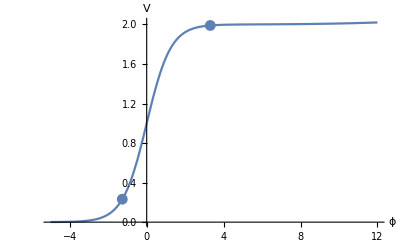

At n = 0, ϵ1 = 0.998113

ns[60] = 0.964795

r[60] = 0.00100326

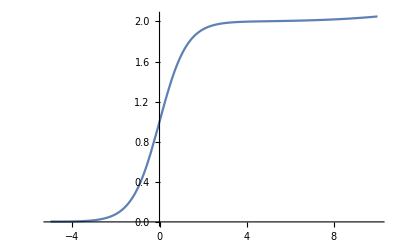

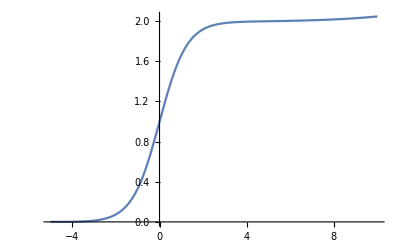

ϕ0list = {-3.35609,-1.26956}

vacuumArray = {}

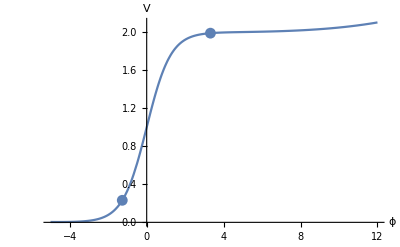

At n = 0, ϵ1 = 0.995964

ns[60] = 0.965528

r[60] = 0.00103003

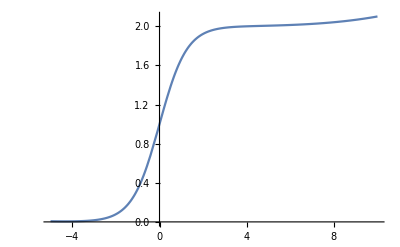

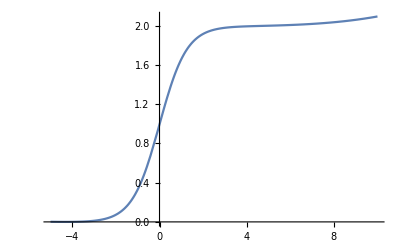

ϕ0list = {-3.08992,-1.27054}

vacuumArray = {}

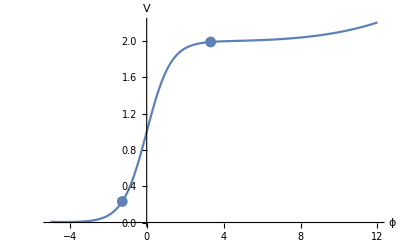

At n = 0, ϵ1 = 0.998314

ns[60] = 0.96645

r[60] = 0.00106513

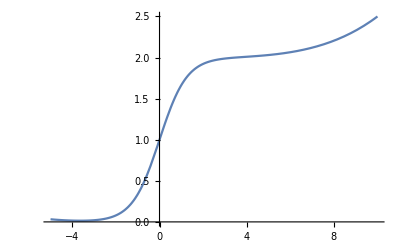

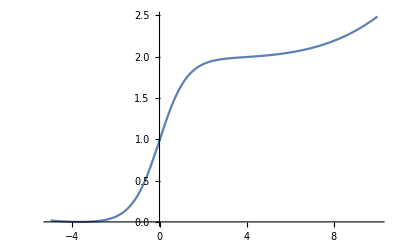

ϕ0list = {-2.48447,-1.27874}

vacuumArray = {}

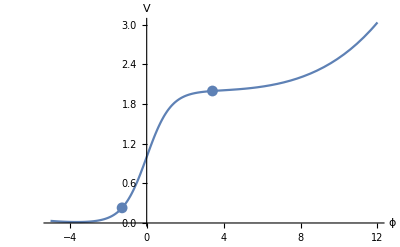

At n = 0, ϵ1 = 0.996346

ns[60] = 0.973964

r[60] = 0.00139413

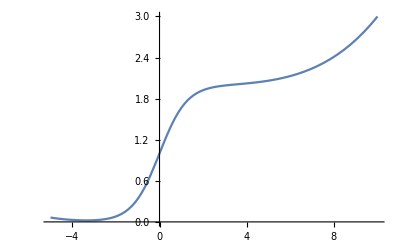

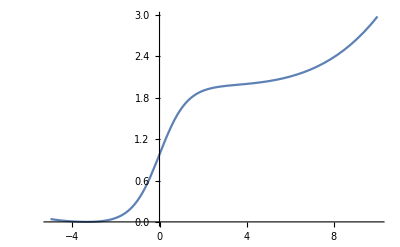

ϕ0list = {-2.22285,-1.28998}

vacuumArray = {}

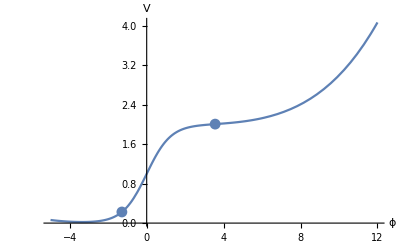

At n = 0, ϵ1 = 0.98993

ns[60] = 0.983695

r[60] = 0.00197039

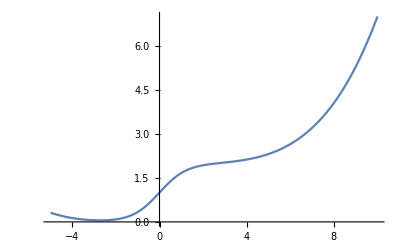

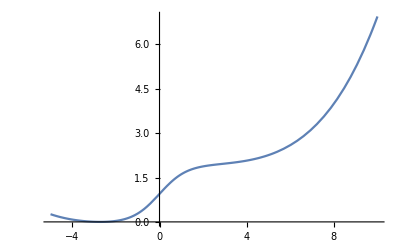

ϕ0list = {}

vacuumArray = {}

ϕ0=-∞

ABORTED

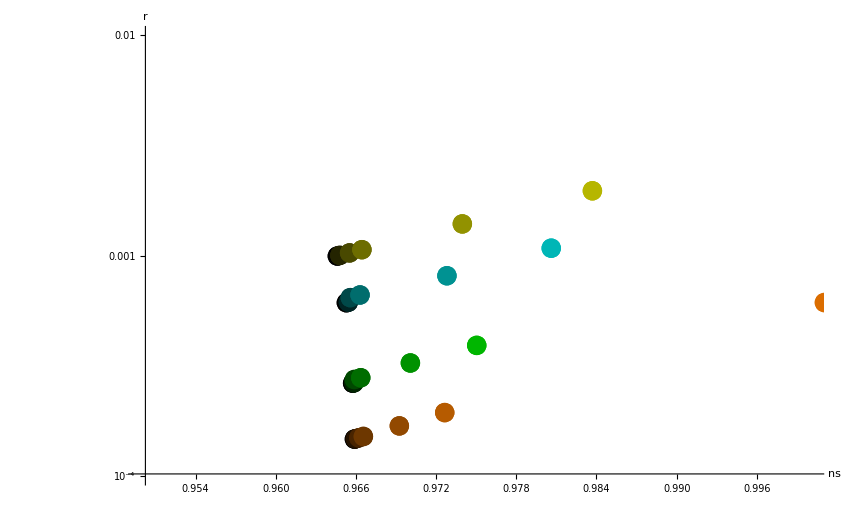

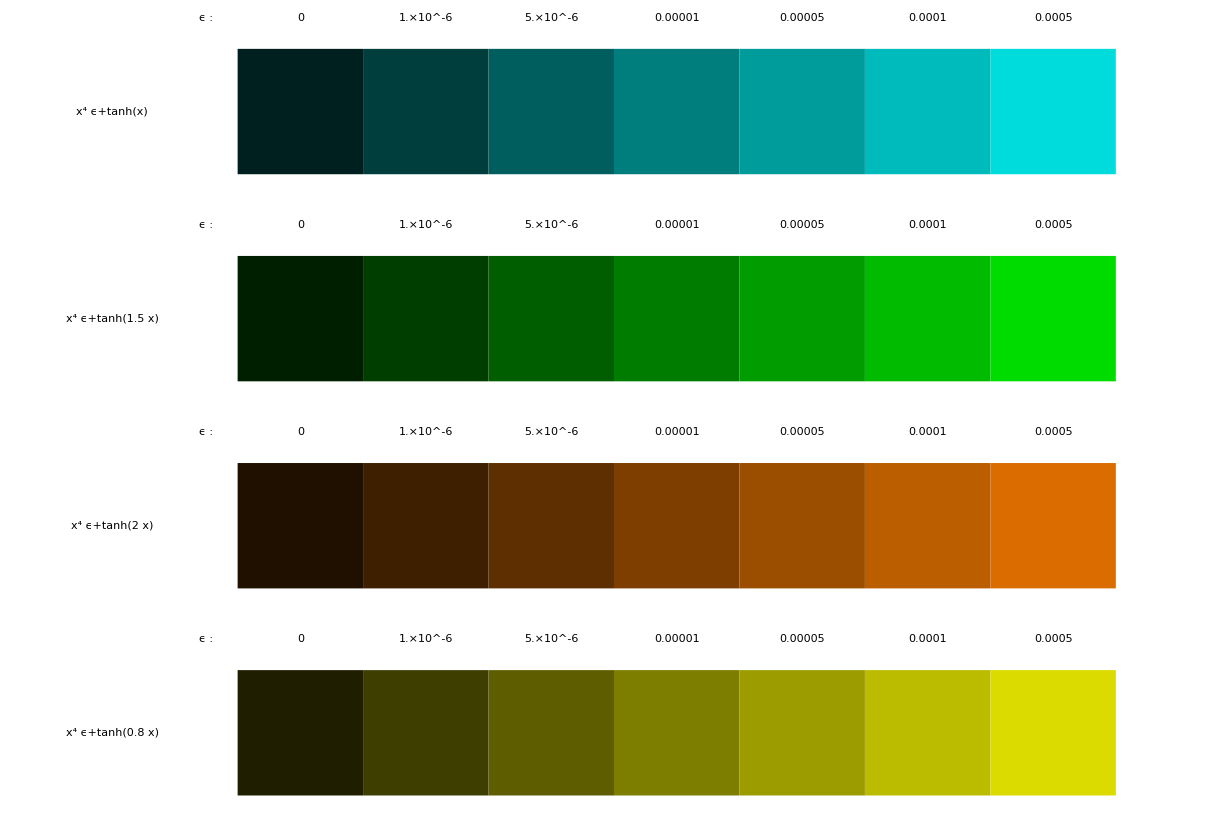

```mathematica
ϵList={0,0.000001,0.00001,0.0001,0.000005,0.00005,0.0005};
bList={1,1.5,2,0.8};
bcList={Cyan,Green,Orange,Yellow};
masterPltList={};legList={};
Do[
v[x_]:=Tanh[bList[[ii]]*x];
{aList,nsList,rList,pltList,legend}=perturbPlot[v,ϵList,bcList[[ii]]];
masterPltList=Join[masterPltList,pltList];
AppendTo[legList,legend];
,{ii,1,Length[bList]}];
Show[masterPltList]
Show[GraphicsColumn[legList]]
```